#### A collection of challenging elastic maps T for finding the closest-Sigma-to-T. The issues pertain to using the built-in Mathematica function NMinimize. ES_FindSymGroups.nb calls GetTempAndθ0σ0ϕ0, which calls NMinimize. INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, BC_ChooseTmat.nb, then this notebook

```mathematica
WantDetails="WantDetails";
```

#### Function to minimize over a localized square patch

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"];
```

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

## Example 1: Brown map

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is t = 0.7 on the segment from TRIG to CUBE.

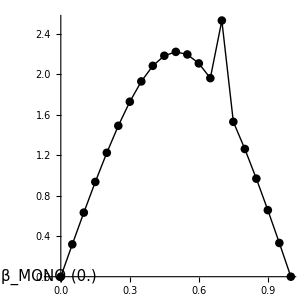

#### closest to MONO (we do not actually need this) Minimization is CORRECT

```mathematica
OutputFor[Tmat,MONO]
```

```mathematica
Show[{ContourPlot[Alpha[Tmat,{θ,ϕ},MONO]/Degree,{θ,1.55,1.8},{ϕ,2.2,2.4},Contours->Automatic,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[Tmat,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

#### closest to TRIG, closest to CUBE

```mathematica
OutputFor[Tmat,TRIG]
OutputFor[Tmat,CUBE]
```

#### Reconstruct the problematic map.

```mathematica
TmatTRIG=Closest[Tmat,TRIG];
TmatCUBE=Closest[Tmat,CUBE];
Tmatx=0.3TmatTRIG+0.7TmatCUBE;
MatrixForm[TmatTRIG]
MatrixForm[TmatCUBE]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (β = 2.53 vs β = 1.76):

```mathematica
OutputFor[Tmatx,MONO]
```

#### OPTIONAL: Plot the two endpoint maps (and zoom-in on the minima). Note: Mathematica doesn’t plot where the contours are too closely spaced, even though you tell it PlotRange->All.

```mathematica
OutputFor[TmatTRIG,MONO]
OutputFor[TmatCUBE,MONO]
```

```mathematica
Show[{ContourPlot[Alpha[TmatTRIG,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->Automatic,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatTRIG,MONO].{0,0,1}]]}}]},FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

```mathematica
cons=Range[0,10,0.5];
Show[{ContourPlot[Alpha[TmatTRIG,{θ,ϕ},MONO]/Degree,{θ,4.5,4.9},{ϕ,0.5,0.9},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatTRIG,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->300]
```

```mathematica
cons=Range[0,12,2];
Show[{ContourPlot[Alpha[TmatCUBE,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatCUBE,MONO].{0,0,1}]]}}]},FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

```mathematica
cons=Range[0,10,0.5];
Show[{ContourPlot[Alpha[TmatCUBE,{θ,ϕ},MONO]/Degree,{θ,4.7,5.1},{ϕ,0.6,1.0},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatCUBE,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->300]
```

#### CORRECT MINIMUM (β = 1.76): Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.3π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 2.53): Blue patch (green point) on the equator and its antipode region:

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### More detailed plot of the contours (hover the mouse over any contour)

```mathematica
ContourPlot[Alpha[Tmatx,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->Range[2,8],PlotPoints->20,ContourShading->None,AspectRatio->Automatic,ImageSize->700]
```

## Example 2: Mar 17

```mathematica
Tmat = TmatMar17;
```

#### The problematic point is t = 0.2 on the segment from MONO to TRIG.

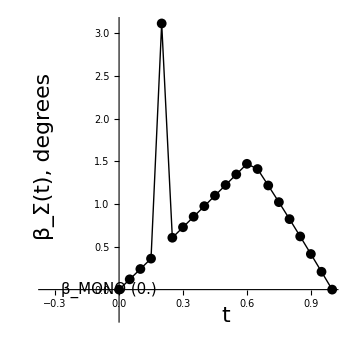

#### Reconstruct the problematic map.

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,XISO]
UXISO=UT[Tmat,XISO];
UforNM1=UXISO;
TMONO=ProjToVSigOfU[Tmat,UforNM1,MONO];
TTRIG=ProjToVSigOfU[Tmat,UforNM1,TRIG];
```

```mathematica
Tmatx=0.8TMONO+0.2TTRIG;
MatrixForm[TMONO]
MatrixForm[TTRIG]
PrintVoigt[Tmatx]
```

#### This fails to find the global minimum (β = 3.11 vs β = 0.48):

```mathematica
OutputFor[Tmatx,MONO]
```

#### CORRECT MINIMUM (β = 0.48): Lower left blue patch (and its antipode):

```mathematica
Flocal[0.4π,0.2π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
```

#### INCORRECT MINIMUM (β = 3.11): Blue patch (green point) on the equator (and its antipode):

```mathematica
Flocal[0.9π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
```